# The Music of Zeta

```mathematica
zetazeroes=Table[N[Im[ZetaZero[i]]],{i,200}];
f2=220;
s1=Graphics[{Thickness[0.002]}~Join~Table[Table[Line[{{n/Log[k],-1.5},{n/Log[k],-.05}}],{n,0,20Log[k]}],{k,2,7}]];
s2=Table[Plot[ Cos[2π Log[k]x]/2+1/2-1.5k,{x,0,20},PlotStyle->{Thickness[0.002]}],{k,2,7}];
s3=Plot[Sum[Cos[2π Log[k]x],{k,2,7}]/5-1,{x,0,20},PlotRange->{-2,-.05},PlotStyle->{Thickness[0.002]}];
line=Graphics[{Thickness[0.002],Line[{{0,-1.5},{20,-1.5}}]}];
line2=Graphics[{Dashed,Thickness[0.002],Line[{{0,-.05},{20,-.05}}]}];
LogPrimorial[x_]:=Plus@@Log[Prime[Range[PrimePi[x]]]];SetAttributes[LogPrimorial,Listable];
ψ[x_]:=Sum[LogPrimorial[x^(1/n)],{n,1,Log[x]/Log[2]}];
chebycurve=Plot[(ψ[E^x]-E^x+Log[2 Pi])E^(-x/2),{x,0,5},PlotStyle->{Thickness[0.002]}];
imgsize=800;
Print[]
```

The Riemann Zeta Function

ζ(s)= ∑_(n=1)^∞ n^-s=1/1^s+1/2^s+1/3^s+1/4^s+1/5^s+...

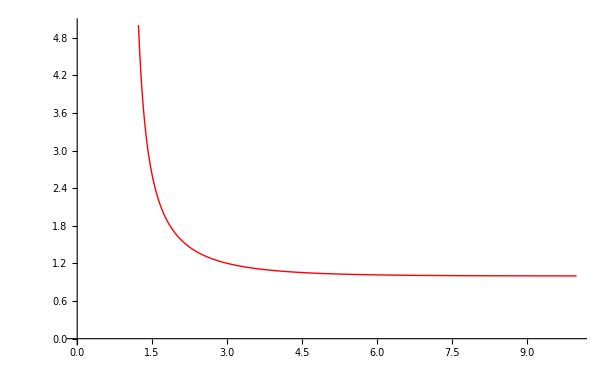

```mathematica
Plot[Zeta[x],{x,1,10},PlotRange->{0,5} ,PlotStyle->{Red,Thick},AxesStyle->Directive[FontSize->30]]
```

Every value has a story to tell.

Every value has a story to tell.

ζ(1) = ∞ ⟺ There are infinitely many primes.

Every value has a story to tell.

ζ(1) = ∞ ⟺ There are infinitely many primes.

The probability that n randomly selected integers have no common factors is 1/(ζ(n)).

Every value has a story to tell.

ζ(1) = ∞ ⟺ There are infinitely many primes.

The probability that n randomly selected integers have no common factors is 1/(ζ(n)).

Special values: ζ(2) = π^2/6, ζ(4)=π^4/90, ζ(6) = π^6/945

Every value has a story to tell.

ζ(1) = ∞ ⟺ There are infinitely many primes.

The probability that n randomly selected integers have no common factors is 1/(ζ(n)).

Special values: ζ(2) = π^2/6, ζ(4)=π^4/90, ζ(6) = π^6/945

ζ(3) = ???

Every value has a story to tell.

What about ζ(2+3i)?

Every value has a story to tell.

What about ζ(2+3i)?

```mathematica
Show[Plot3D[Re[Zeta[x+I y]],{x,1,10},{y,-20,20},PlotRange->{0,3}],ParametricPlot3D[{x,0,Zeta[x]},{x,1,10},AxesStyle->Directive[FontSize->30],PlotStyle->{Red,Thickness[0.01]}],ImageSize->0.9imgsize]
```

-Graphics3D-

Every value has a story to tell.

What about ζ(2+3i)?

Every value has a story to tell.

What about ζ(2+3i)?

What about ζ(0)?

Every value has a story to tell.

What about ζ(2+3i)?

What about ζ(0)? (“=1+1+1+1+1+...”)

Every value has a story to tell.

What about ζ(2+3i)?

What about ζ(0)? (“=1+1+1+1+1+...”)

What about ζ(-1)?

Every value has a story to tell.

What about ζ(2+3i)?

What about ζ(0)? (“=1+1+1+1+1+...”)

What about ζ(-1)? (“=1+2+3+4+5+...”)

Every value has a story to tell.

What about ζ(2+3i)?

What about ζ(0)? (“=1+1+1+1+1+...”)

What about ζ(-1)? (“=1+2+3+4+5+...”)

When does ζ(z)=0, and why do people care?

Musical Notes

```mathematica
keyboard=Import["C:\\Users\\Jonathan\\Documents\\0 Jobs\\MC16\\keyboard-piano.JPG",ImageSize->imgsize];
Show[keyboard]
```

-Graphics-

```mathematica
time=0.3;
f2=220;
play12[n_]:=Play[Sin[2^(n/12) f2 2 Pi t],{t,n*time,(n+1)*time}];
play11[n_]:=Play[Sin[2^(n/8) f2 2 Pi t],{t,n*time,(n+1)*time}];
Row[{Sound[play12@@@{{0},{2},{4},{5},{7},{9},{11},{12}}],
time=0.3;
Sound[play12@@@Table[{i},{i,0,12}]],
time=0.5;
Sound[play11@@@Table[{i},{i,0,8}]]}]
```

-Graphics--Graphics--Graphics-

Musical Notes

```mathematica
num[n_]:=Graphics[Text[Style[n,FontSize->36]]]
ImageCompose[keyboard,{num[1],num[2],num[4],num[8]},{Scaled[{0.03,0.15}],Scaled[{0.346,0.15}],Scaled[{0.66,0.15}],Scaled[{0.975,0.15}]}]
```

-Graphics-

```mathematica
time=0.3;
f2=220;
play12[n_]:=Play[Sin[2^(n/12) f2 2 Pi t],{t,n*time,(n+1)*time}];
play11[n_]:=Play[Sin[2^(n/8) f2 2 Pi t],{t,n*time,(n+1)*time}];
Row[{Sound[play12@@@{{0},{2},{4},{5},{7},{9},{11},{12}}],
time=0.3;
Sound[play12@@@Table[{i},{i,0,12}]],
time=0.5;
Sound[play11@@@Table[{i},{i,0,8}]]}]
```

-Graphics--Graphics--Graphics-

```mathematica
piano=ImageRotate[Import["C:\\Users\\Jonathan\\Documents\\0 Jobs\\MC16\\piano.jpg",ImageSize->imgsize*3/4]];
Show[piano]
```

-Graphics-

The Grand Piano

```mathematica
exp=Plot[5^(-x),{x,-1,2},ImageSize->100,AspectRatio->Automatic,PlotStyle->{Cyan,Thickness[0.015]},Axes->None];
ImageCompose[piano,exp,Scaled[{0.66,0.65}]]
```

-Graphics-

The Graph Piano

```mathematica
num[n_]:=Graphics[Text[Style[n,FontSize->36]]]
ImageCompose[keyboard,{num[1],num[2],num[4],num[8]},{Scaled[{0.03,0.15}],Scaled[{0.346,0.15}],Scaled[{0.66,0.15}],Scaled[{0.975,0.15}]}]
```

-Graphics-

```mathematica
ImageCompose[keyboard,{num[1],num[2],num[4],num[8],num[3],num[5],num[6],num[7]},{Scaled[{0.03,0.15}],Scaled[{0.346,0.15}],Scaled[{0.66,0.15}],Scaled[{0.975,0.15}],Scaled[{0.525,0.15}],Scaled[{0.75,0.15}],Scaled[{0.84,0.15}],Scaled[{0.91,0.15}]}]
```

-Graphics-

The “harmonic scale”
Frequencies: {1, 2, 3, 4, 5, 6, ...}

```mathematica
time=0.5;
f=110;
play[n_]:=Play[Sin[(n+1) f 2 Pi t],{t,n*time,(n+1)*time}];
Sound[play@@@Table[{n},{n,0,15}]]
```

-Graphics-

Goal: We want a scale with both equal division and harmonics.

Equal Division: there is a single step size, b, such that every pitch in our scale is of the form b^k for some k.

Harmonics: All whole numbers are in our scale.

Goal: We want a scale with both equal division and harmonics.

Equal Division: there is a single step size, b, such that every pitch in our scale is of the form b^k for some k.

Harmonics: All whole numbers are in our scale.

That is: we need b such that for any whole number n, 
there exists a whole number k_n such that b^k_n=n.

When is x=1/(log b) close to an integer multiple of 1/(log n)?

```mathematica
Manipulate[Show[line,line2,If[u=="add",s1,Graphics[]],If[u=="curves"||u=="curveadd",s2,Graphics[]],If[u=="curveadd",s3,Graphics[]],Graphics[Table[{Inset[Text[Style[1/log[k],FontSize->28]],{-1,-1.5k}],Line[{{0,-1.5k},{20,-1.5k}}]}~Join~Table[{Thickness[0.003],Line[{{n/Log[k],-1.5k-0.2},{n/Log[k],-1.5k+0.2}}]},{n,0,20Log[k]}],{k,2,7}]],ImageSize->imgsize],{u,{"none","add","curves","curveadd"}}]
```

Plot of Re[ζ(a+ i x(2π/log 2))]
Maximum near k ⟺ Dividing an octave into k equal steps approximates many harmonics

```mathematica
Manipulate[Plot[Re[Zeta[a+I s 2π/Log[2]]],{s,0,domain},AxesStyle->Directive[24], PlotStyle->Thickness[0.005],PlotRange->If[a==1.4,{0.4,2.1},All],ImageSize->3/4*imgsize],{domain,{15,55}},{a,{10,4,2,1.4,1,1/2}},ControlType->SetterBar]
```

The “logarithmic scale”

Frequencies: {log2/log2,log3/log2,log4/log2,log5/log2,log6/log2,...}

```mathematica
time=0.5;
f=110;
play[n_]:=Play[Sin[Log[n+2]/Log[2] f 2 Pi t],{t,n*time,(n+1)*time}];
Sound[play@@@Table[{n},{n,0,14}]]
```

-Graphics-

The “logarithmic scale”

Frequencies: {log2/log2,log3/log2,log4/log2,log5/log2,log6/log2,...}

```mathematica
time=0.5;
f=110;
play[n_]:=Play[Sin[Log[n+2]/Log[2] f 2 Pi t],{t,n*time,(n+1)*time}];
Sound[play@@@Table[{n},{n,0,14}]]
```

-Graphics-

The Riemann Zeta function along vertical lines is a sum of sine waves.

Let’s listen.

Plot of  ∑_(n=1)^M n^-z (“truncated zeta series”)

```mathematica
lineat[a_,M_,col_]:=ParametricPlot3D[{a,x,Sum[Re[1/n^(a+I x)],{n,1,M}]},{x,-20,20},AxesStyle->Directive[FontSize->30],PlotStyle->{col,Thickness[0.01]}];
BigPlots[M_]:=Show[Plot3D[Sum[Re[1/n^(a+I t)],{n,1,M}],{a,-1,5},{t,-20,20},PlotRange->{-5,5},ImageSize->imgsize],lineat[2,M,Blue],lineat[1,M,Red],lineat[1/2,M,Blue]]//Rasterize;
BPlots=SparseArray[#->BigPlots[#]&/@{2,3,5,10,30,200,1000}];
Manipulate[BPlots[[M]],{M,{2,3,5,10,30,200,1000}},ControlType->SetterBar]
```

Plot of  ∑_(n=1)^M n^(-(a+i x)) (“truncated zeta series”)

```mathematica
Manipulate[Plot[Sum[Re[1/n^(a+I t)],{n,1,M}],{t,-40,40},PlotStyle->Thickness[0.004],ImageSize->800],{M,1,100,1},{a,{1.6,1,0.5}}]
```

```mathematica
xvals={2,1.4,1,0.5};
Nvals={2,3,6,20,50,100,500,1000};Grid[Array[Play[Sum[Re[1/n^(xvals[[#2]]+1000I t)],{n,1,Nvals[[#1]]}],{t,0,1}]&,{Length[Nvals],Length[xvals]}]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Play[(0.0316/t+(0.0330-0.0316)t)Sin[1000Log[1000]t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sum[Re[1/n^(1/2+1000I t)],{n,1,1000}]-(0.0316/t+(0.0330-0.0316)t)Sin[1000Log[1000]t],{t,0.01,1}]
```

-Graphics-

Plot of truncated zeta series and Re[ζ(a+i x)]

```mathematica
Manipulate[Plot[{Re[Zeta[x+I t ]],Sum[Re[1/n^(x+I t)],{n,1,m}]},{t,-40,40},PlotStyle->Thickness[0.005],ImageSize->imgsize],{m,1,100,1},{x,{2,1.4,1,0.5}}]
```

```mathematica
lineat2[a_,col_]:=ParametricPlot3D[{a,x,Re[Zeta[a+I x]]},{x,-20,20},AxesStyle->Directive[FontSize->30],PlotStyle->{col,Thickness[0.01]}];
zetaplot=Show[Plot3D[Re[Zeta[a+I t]],{a,-1,5},{t,-20,20},PlotRange->{-5,5},ImageSize->imgsize],lineat2[2,Blue],lineat2[1,Red],lineat2[1/2,Blue]]//Rasterize ;
Manipulate[ImageCompose[zetaplot,{BPlots[[1000]],x}],{x,1,0}]
```

π(x)= number of primes ≤x

```mathematica
Manipulate[Plot[PrimePi[x],{x,0,m},AspectRatio->1,PlotStyle->Thickness[0.005],ImageSize->imgsize*1/2],{m,{15,100,1000}}]
```

ψ(x)=  ∑_(n=p^k<x) log(p)

```mathematica
Manipulate[Plot[ψ[x],{x,0,m},AspectRatio->1,PlotStyle->Thickness[0.005],ImageSize->imgsize*1/2],{m,{15,100,1000}}]
```

Looks like ψ(x)≈x.
What is x-ψ(x)?

Looks like ψ(x)≈x.
What is x-ψ(x)?

```mathematica
Manipulate[Plot[x-ψ[x],{x,0,m},AspectRatio->1,PlotStyle->Thickness[0.005]],{m,{10,100,1000}}]
```

Looks like ψ(x)≈x.
What is x-ψ(x)?

```mathematica
Manipulate[Plot[x-ψ[x],{x,0,m},AspectRatio->1,PlotStyle->Thickness[0.005]],{m,{10,100,1000}}]
```

Do we see... waves?

(Hans Carl Friedrich von Mangoldt, 1895):

x-ψ(x)= ∑_(ρ: ζ(ρ)=0) x^ρ/ρ+log 2π

The “zeta scale”

Frequencies: {Im[ρ_1],Im[ρ_2],Im[ρ_3],...}

```mathematica
time=0.3;
f=110;
play[n_]:=Play[Sin[zetazeroes[[n+1]]/zetazeroes[[1]] f 2 Pi t],{t,n*time,(n+1)*time}];
Sound[play@@@Table[{n},{n,0,15}]]
```

-Graphics-

The Logarithmic Chebyshev error is a sum of sine waves.

Let’s listen.

Playing the Chebyshev Error

```mathematica
Play[x1=x;(ψ[100000x]-100000x+Log[2 Pi]),{x,0,1}]
```

-Graphics-

Playing the Chebyshev Error along a logarithmic scale...

```mathematica
Play[x1=x;(ψ[200^x]-200^x+Log[2 Pi])/Sqrt[200]^x,{x,0,2}]
```

-Graphics-

Logarithmic Chebyshev Error vs. the sum of zeta zeroes

```mathematica
Manipulate[Show[chebycurve,Plot[-Sum[2Re[E^(I x zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,1,m}],{x,0,5},PlotStyle->{Thickness[0.005],Orange}]],{m,1,100,1}]
```

Part::partd: Part specification zetazeroes ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in chebycurve, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Part::partd: Part specification zetazeroes ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in chebycurve, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Sum of first {1,2,3,4,5,10} zeroes

```mathematica
{Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,1}],{x,0,1}],
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,2}],{x,0,1}],
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,3}],{x,0,1}],
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,4}],{x,0,1}],
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,5}],{x,0,1}],
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,10}],{x,0,1}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Sum of first {50,100,200} zeroes

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,50}],{x,0.01,1.01}]
```

-Graphics-

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,100}],{x,0.01,1.01}]
```

-Graphics-

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,200}],{x,0.01,1.01}]
```

-Graphics-

Sum of first {50,100,200} zeroes

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,50}],{x,0.01,1.01}]
```

-Graphics-

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,100}],{x,0.01,1.01}]
```

-Graphics-

```mathematica
Play[Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,200}],{x,0.01,1.01}]
```

-Graphics-

The Eerie Decibels of the Irreducibles

What if one of the zeroes had Re[ρ]>1/2?

```mathematica
Play[Re[E^(.3x)E^(I (50x) zetazeroes[[21]])/(0.51+I zetazeroes[[21]])]+Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,20}],{x,0,10}]
```

-Graphics-

What if one of the zeroes had Re[ρ]>1/2?

```mathematica
Play[Re[E^(.3x)E^(I (50x) zetazeroes[[21]])/(0.51+I zetazeroes[[21]])]+Sum[Re[E^(I (50x) zetazeroes[[i]])/(1/2+I zetazeroes[[i]])],{i,20}],{x,0,10}]
```

-Graphics-

Riemann Hypothesis: 
All notes of the zeta scale are played 
equally loudly in the chord of the primes.